```mathematica
Numerical methods for Stochastic Differential Equations
```

```mathematica
β=0.3;
α=100;
σ=1;
aFun[t_,x_]:=-β(x-α)
bFun[t_,x_]:= σ √x
```

```mathematica
eulerMaruyama[t0_,x0_,a_,b_]:=Module[{x=x0,t=t0,t1,solution={x0}},t1=t;Do[t=t1;t1++;x=x+a[t,x]*(t1-t)+b[t,x]*RandomVariate[NormalDistribution[0,1]]*√(t1-t);AppendTo[solution,x],20];solution]
```

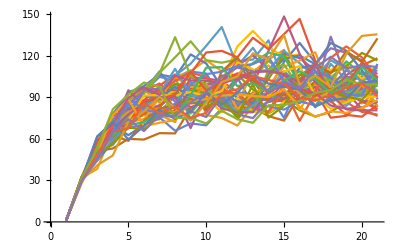

```mathematica
res=Table[eulerMaruyama[0,1,aFun,bFun],50];
ListLinePlot[res,PlotRange->{Automatic,Full}]
```

2 σ/(√(2β))- Ширина интервала сходимости процесса О-У.

```mathematica
2*σ/√(β*2)//N
```

3.87298

Runge-Kutt’s method

```mathematica
rungeKutt[t0_,x0_,a_,b_]:=Module[{x=x0,t=t0,t1,solution={x0},k1,k2,k3},t1=t;Do[t=t1;t1++;k1=x+a[t,x]*(t1-t)+b[t,x]*RandomVariate[NormalDistribution[0,1]]*√(t1-t);
k2=x+a[t,k1]*(t1-t)+b[t,k1]*√(t1-t);
k3=x+a[t,k2]*(t1-t)+b[t,k2]*√(t1-t);x=x+1/2(a[t,k1]+a[t,x])*(t1-t)+1/4(b[t,k2]+b[t,k3]+2b[t,x])*RandomVariate[NormalDistribution[0,1]]*√(t1-t)+1/4(b[t,k2]-b[t,k3])(RandomVariate[NormalDistribution[0,1]]*√(t1-t)-(t1-t))/√(t1-t);AppendTo[solution,x],20];solution]
```

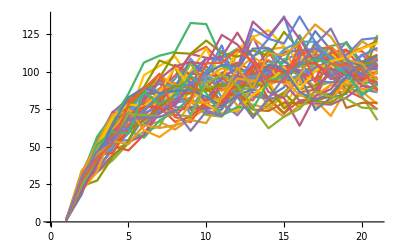

```mathematica
res2=Table[rungeKutt[0,1,aFun,bFun],50];
ListLinePlot[res2,PlotRange->{Automatic,Full}]
```

Numerical modeling of systems of SDE’s

```mathematica
milstein[t0_,x10_,x20_,a_,b_,b11_,b12_,b21_,b22_]:=Module[{n=30,dt=0.1,γ=0.3,um1=1,um2=1,x1=x10,x2=x20,solution1={},solution2={},q=50,b1=b11*(b11+b21),g1=b12*(b11+b21),b2=b21*(b11+b21),g2=b22*(b11+b21),r1=b11*(b12+b22),a1=b12*(b12+b22),r2=b21*(b12+b22),a2=b22*(b12+b22),w,v,s1,s2,u11,u12,u21,u22,u01,u02,f1,f2},Do[w=RandomVariate[NormalDistribution[0,1],q+1];v=RandomVariate[NormalDistribution[0,1],q+1];s1=w[[1]]*v[[1]];s2=w[[1]]*v[[1]];Do[s1=s1+(1/(√(4*j^2-1)))+(w[[j]]+v[[j+1]]-w[[j+1]]*v[[j]]);s2=s2+(1/(√(4*j^2-1)))+(v[[j]]+w[[j+1]]-v[[j+1]]*w[[j]]);,{j,1,q}];
u21=0.5*dt*s1;u12=0.5*dt*s2;u01=v[[1]]*√dt;u02=w[[1]]*√dt;u11=0.5*(u01^2-dt);u22=0.5*(u02^2-dt);f1=ⅇ^(γ*(x1+x2));f2=ⅇ^(0.5*γ*(x1+x2));
x1=x1+um1*dt+f2*(b11*u01+b12*u02)+0.5*γ*f1*(b1*u11+r1*u21+g1*u12+a1*u22);
x2=x2+um2*dt+f2*(b21*u01+b22*u02)+0.5*γ*f1*(b2*u11+r2*u21+g2*u12+a2*u22);AppendTo[solution1,x1];AppendTo[solution2,x2],{i,1,n}];{solution1,solution2}
]
```

```mathematica
res=milstein[0,1,1,aFun,bFun,0.1,0.05,-0.05,0.3];
tList=Range[30];
```

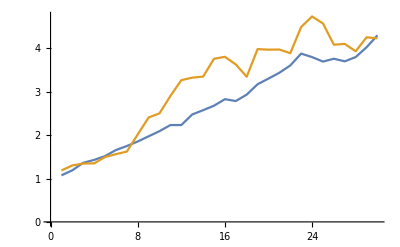

```mathematica
ListLinePlot[{res[[1]],res[[2]]}]
```